Fourier transform of a Gaussian is a Gaussian

```mathematica
A[x_] = A0 Exp[-x^2/w0^2]; (*Gaussian profile of a laser beam*)
```

```mathematica
Integrate[A[x]Exp[ⅈ k x],{x,-∞,∞}]
```

ConditionalExpression[(A0 ⅇ^(-1/4 k^2 w0^2) √π)/(√(1/w0^2)),Re[w0^2]>0]

What if the Gaussian is clipped?

```mathematica
Integrate[A[x]Exp[ⅈ k x],{x,-a,a}]
```

1/2 A0 ⅇ^(-1/4 k^2 w0^2) √π w0 (Erf[a/w0-(ⅈ k w0)/2]+Erf[a/w0+(ⅈ k w0)/2])

```mathematica
A0=1; w0 = 1; a = w0/2;
```

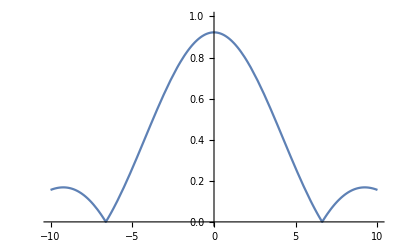

```mathematica
scl = 20;
Plot[Abs[1/2 A0 ⅇ^(-1/4 k^2 w0^2) √π w0 (Erf[a/w0-(ⅈ k w0)/2]+Erf[a/w0+(ⅈ k w0)/2])], {k,-scl*a,scl*a},PlotRange->{{-scl*a,scl*a},{0,1}}]
```

Power in a clipped Gaussian beam:

```mathematica
Integrate[r Exp[-2 r^2/w^2],{r,0,a}]/Integrate[r Exp[-2 r^2/w^2],{r,0,∞}]
```

ConditionalExpression[1-ⅇ^(-(2 a^2)/w^2),Re[w^2]>0]

```mathematica
1-ⅇ^(-(2 a^2)/w^2)/.a-> w/4//N
```

0.117503

```mathematica
1-ⅇ^(-(2 a^2)/w^2)/.a-> w/2//N
```

0.393469

```mathematica
1-ⅇ^(-(2 a^2)/w^2)/.a-> w//N
```

0.864665